# Tweets of the US Senators of the 115th Congress

Source: https://dataverse.harvard.edu/file.xhtml?fileId=3354806&version=3.0

Set options used for all ListPlots in this notebook:

```mathematica
SetOptions[ListPlot,PlotTheme->"Detailed",ImageSize->Large,PlotRange->All];
SetOptions[DateListPlot,PlotTheme->"Detailed",ImageSize->Large,PlotRange->All];
```

Set the directory:

```mathematica
SetDirectory@NotebookDirectory[]
```

D:\github\tweets-115th-congress

Get the files:

```mathematica
files=Apply[Join,FileNames["*.json",FileNameJoin[{"US115thcongress",#}]]&/@{"Democrat","Republican","Independent"}];
```

Check for the number of senators that have tweeted:

```mathematica
Length[files]
```

100

Import the twitter archive for each senator:

```mathematica
dataset=Dataset[Association[StringReplace[FileBaseName[#],"_twitter"->""]->Dataset[Map[Association,Import[#]]]&/@files]];
```

Display a twitter archive for a randomly chose senator:

```mathematica
RandomChoice[dataset]
```

Dataset[<>]

Get the dataset for a specific senator

```mathematica
dataset["SteveDaines"]
```

Dataset[<>]

#### Who tweeted the most?

Get the number of tweets and sort them:

```mathematica
numberTweets=dataset[ReverseSort,Length]
```

Dataset[<>]

The most frequent tweeters:

```mathematica
Take[numberTweets,5]
```

Dataset[<>]

The least frequent tweeters:

```mathematica
Take[numberTweets,-5]
```

Dataset[<>]

Due to an error in the source data, senator Sanders only has one tweet (pointing to the correct @SenSanders twitter handle):

```mathematica
dataset["SenatorSanders"]
```

Dataset[<>]

Plot the number of tweets so they are easy to compare:

```mathematica
ListPlot[numberTweets]
```

-Graphics-

#### Who has the most ‘likes’ ?

Compute the ‘likes’ for one senator. Use ToExpression to turn the ‘likes’ strings into integers

```mathematica
dataset["SenWhitehouse"][Total[Map[ToExpression,#]]&,"likes"]
```

1747155

Compute the number of ‘likes’ for each senator and sort them:

```mathematica
numberLikes=ReverseSort@Map[#[Total[Map[ToExpression,#]]&,"likes"]&,dataset]
```

Dataset[<>]

The senators with the most ‘likes’:

```mathematica
Take[numberLikes,5]
```

Dataset[<>]

The senators with the least ‘likes’:

```mathematica
Take[numberLikes,-5]
```

Dataset[<>]

```mathematica
ListPlot[numberLikes,ImageSize->900]
```

-Graphics-

#### Who has the most ‘retweets’ ?

Compute the ‘retweets’ for one senator. Use ToExpression to turn the ‘likes’ strings into integers

```mathematica
dataset["brianschatz"][Total[Map[ToExpression,#]]&,"retweets"]
```

2096478

Compute the number of ‘retweets’ for each senator and sort them:

```mathematica
numberRetweets=ReverseSort@Map[#[Total[Map[ToExpression,#]]&,"retweets"]&,dataset]
```

Dataset[<>]

The senators with the most ‘retweets’:

```mathematica
Take[numberRetweets,5]
```

Dataset[<>]

The senators with the least ‘retweets’:

```mathematica
Take[numberRetweets,-5]
```

Dataset[<>]

Plot the ‘retweets’ for each senator:

```mathematica
ListPlot[numberRetweets]
```

-Graphics-

#### Who has the most ‘replies’ ?

Compute the ‘replies’ for one senator. Use ToExpression to turn the ‘likes’ strings into integers

```mathematica
dataset["SenateMajLdr"][Total[Map[ToExpression,#]]&,"retweets"]
```

403353

Compute the number of ‘replies’ for each senator and sort them:

```mathematica
numberReplies=ReverseSort@Map[#[Total[Map[ToExpression,#]]&,"replies"]&,dataset]
```

Dataset[<>]

The senators with the most ‘replies’:

```mathematica
Take[numberReplies,5]
```

Dataset[<>]

The senators with the least ‘replies’:

```mathematica
Take[numberReplies,-5]
```

Dataset[<>]

Plot the ‘replies’ for each senator:

```mathematica
ListPlot[numberReplies]
```

-Graphics-

#### What are the total number of tweets per day?

Get the daily counts of tweets for all senators combined:

```mathematica
counts=KeySort[Counts@Map[StringTake[#,10]&,Join@@Values[Normal[Map[Normal[#[All,"timestamp"]]&,dataset]]]]];
```

Plot the number of tweets per day. The number of tweets has grown over time (a lot). Tweets before the actual start date of the 115th Congress are older tweets that were retweeted.

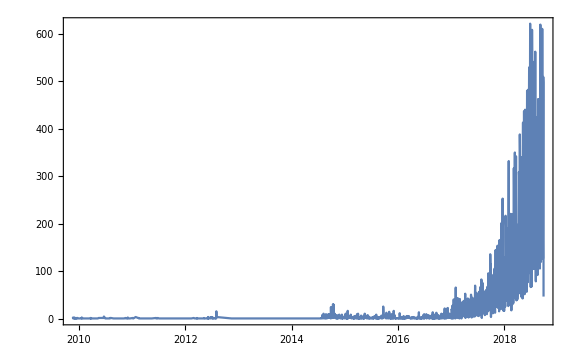

```mathematica
DateListPlot[counts]
```

Plot the moving average of tweets per senator per day. Note the increase from almost zero to about 3 at the end of the time period:

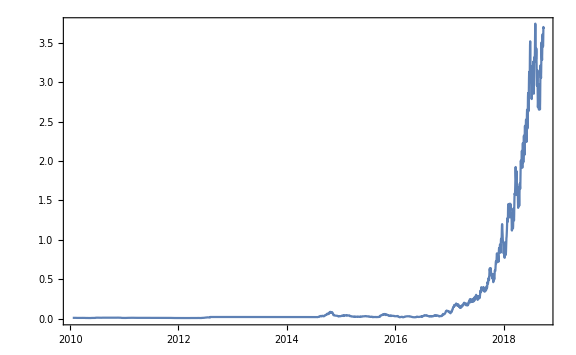

```mathematica
DateListPlot[MovingAverage[counts/100.0,25],ImageSize->Large]
```

#### What are the most used #HashTags?

Get the hashtags used by each senator and tally them by their frequency of use:

```mathematica
hashtags=Map[#[ReverseSort@Counts@Flatten@StringCases[#,"#"~~WordCharacter..]&,"text"]&,dataset];
```

Look at the results for a few senators:

```mathematica
RandomSample[hashtags,3]
```

Dataset[<>]

Overall hashtag frequency:

```mathematica
allHashtags=ReverseSort@Counts@Flatten@Map[Flatten@StringCases[#,"#"~~WordCharacter..]&,tweetText];
```

Most popular, showing common topics such as the tax reform bill, net neutrality, supreme court, farm bill, the state of the union, and the deferred action for childhood arrivals policy:

```mathematica
Dataset@Take[allHashtags,100]
```

Dataset[<>]

A word cloud of the most popular hashtags

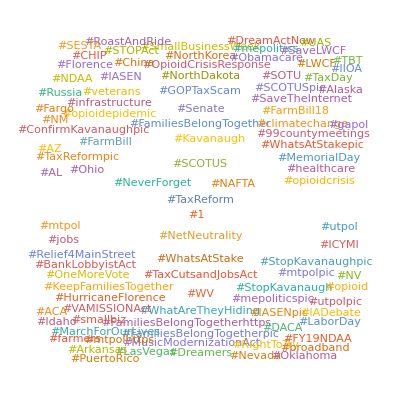

```mathematica
WordCloud[Take[allHashtags,100]]
```

Plot all the top 1000  hashtags by their frequency:

```mathematica
ListPlot[Take[allHashtags,1000]]
```

-Graphics-